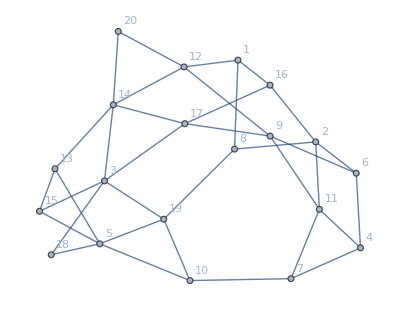

```mathematica
edges={UndirectedEdge[1,8],UndirectedEdge[1,12],UndirectedEdge[1,16],UndirectedEdge[2,6],UndirectedEdge[2,8],UndirectedEdge[2,11],UndirectedEdge[2,16],UndirectedEdge[3,14],UndirectedEdge[3,15],UndirectedEdge[3,17],UndirectedEdge[3,18],UndirectedEdge[3,19],UndirectedEdge[4,6],UndirectedEdge[4,7],UndirectedEdge[4,11],UndirectedEdge[5,10],UndirectedEdge[5,13],UndirectedEdge[5,15],UndirectedEdge[5,18],UndirectedEdge[5,19],UndirectedEdge[6,9],UndirectedEdge[7,10],UndirectedEdge[7,11],UndirectedEdge[8,19],UndirectedEdge[9,11],UndirectedEdge[9,12],UndirectedEdge[9,17],UndirectedEdge[10,19],UndirectedEdge[12,14],UndirectedEdge[12,20],UndirectedEdge[13,14],UndirectedEdge[13,15],UndirectedEdge[14,17],UndirectedEdge[14,20],UndirectedEdge[16,17]};
mygraph = Graph[edges,VertexLabels->"Name"]
```

```mathematica
adjacencyList=AdjacencyList[mygraph]

(*Вывод результата*)
TableForm[adjacencyList,TableHeadings->{VertexList[mygraph],None}]
```

{{8,12,16},{1,2,19},{1,14,9,20},{1,2,17},{8,16,6,11},{2,4,9},{2,4,7,9},{14,15,17,18,19},{12,3,17,13,20},{3,5,13},{16,3,14,9},{3,5},{8,3,5,10},{6,11,7},{11,4,10},{15,18,19,10,13},{19,7,5},{14,15,5},{12,6,11,17},{12,14}}

1 | 8 | 12 | 16 |  | 
8 | 1 | 2 | 19 |  | 
12 | 1 | 14 | 9 | 20 | 
16 | 1 | 2 | 17 |  | 
2 | 8 | 16 | 6 | 11 | 
6 | 2 | 4 | 9 |  | 
11 | 2 | 4 | 7 | 9 | 
3 | 14 | 15 | 17 | 18 | 19
14 | 12 | 3 | 17 | 13 | 20
15 | 3 | 5 | 13 |  | 
17 | 16 | 3 | 14 | 9 | 
18 | 3 | 5 |  |  | 
19 | 8 | 3 | 5 | 10 | 
4 | 6 | 11 | 7 |  | 
7 | 11 | 4 | 10 |  | 
5 | 15 | 18 | 19 | 10 | 13
10 | 19 | 7 | 5 |  | 
13 | 14 | 15 | 5 |  | 
9 | 12 | 6 | 11 | 17 | 
20 | 12 | 14 |  |  |

Здесь список смежности представлен в виде таблицы: Ребро -> Смежные к нему
Составим матрицу смежности:

```mathematica
AdjacencyMatrix[mygraph] //MatrixForm
```

(0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

Составим матрицу инциденций используя встроенную функцию:

```mathematica
IncidenceMatrix[mygraph] //MatrixForm
```

(1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0)

Составим матрицу расстояний в графе:

```mathematica
myDistanceMatrix = GraphDistanceMatrix[mygraph];
myDistanceMatrix//MatrixForm
```

(0 | 1 | 1 | 1 | 2 | 3 | 3 | 3 | 2 | 4 | 2 | 4 | 2 | 4 | 4 | 3 | 3 | 3 | 2 | 2
1 | 0 | 2 | 2 | 1 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 1 | 3 | 3 | 2 | 2 | 3 | 3 | 3
1 | 2 | 0 | 2 | 3 | 2 | 2 | 2 | 1 | 3 | 2 | 3 | 3 | 3 | 3 | 3 | 4 | 2 | 1 | 1
1 | 2 | 2 | 0 | 1 | 2 | 2 | 2 | 2 | 3 | 1 | 3 | 3 | 3 | 3 | 4 | 4 | 3 | 2 | 3
2 | 1 | 3 | 1 | 0 | 1 | 1 | 3 | 3 | 4 | 2 | 4 | 2 | 2 | 2 | 3 | 3 | 4 | 2 | 4
3 | 2 | 2 | 2 | 1 | 0 | 2 | 3 | 3 | 4 | 2 | 4 | 3 | 1 | 2 | 4 | 3 | 4 | 1 | 3
3 | 2 | 2 | 2 | 1 | 2 | 0 | 3 | 3 | 4 | 2 | 4 | 3 | 1 | 1 | 3 | 2 | 4 | 1 | 3
3 | 2 | 2 | 2 | 3 | 3 | 3 | 0 | 1 | 1 | 1 | 1 | 1 | 4 | 3 | 2 | 2 | 2 | 2 | 2
2 | 3 | 1 | 2 | 3 | 3 | 3 | 1 | 0 | 2 | 1 | 2 | 2 | 4 | 4 | 2 | 3 | 1 | 2 | 1
4 | 3 | 3 | 3 | 4 | 4 | 4 | 1 | 2 | 0 | 2 | 2 | 2 | 4 | 3 | 1 | 2 | 1 | 3 | 3
2 | 3 | 2 | 1 | 2 | 2 | 2 | 1 | 1 | 2 | 0 | 2 | 2 | 3 | 3 | 3 | 3 | 2 | 1 | 2
4 | 3 | 3 | 3 | 4 | 4 | 4 | 1 | 2 | 2 | 2 | 0 | 2 | 4 | 3 | 1 | 2 | 2 | 3 | 3
2 | 1 | 3 | 3 | 2 | 3 | 3 | 1 | 2 | 2 | 2 | 2 | 0 | 3 | 2 | 1 | 1 | 2 | 3 | 3
4 | 3 | 3 | 3 | 2 | 1 | 1 | 4 | 4 | 4 | 3 | 4 | 3 | 0 | 1 | 3 | 2 | 4 | 2 | 4
4 | 3 | 3 | 3 | 2 | 2 | 1 | 3 | 4 | 3 | 3 | 3 | 2 | 1 | 0 | 2 | 1 | 3 | 2 | 4
3 | 2 | 3 | 4 | 3 | 4 | 3 | 2 | 2 | 1 | 3 | 1 | 1 | 3 | 2 | 0 | 1 | 1 | 4 | 3
3 | 2 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 2 | 3 | 2 | 1 | 2 | 1 | 1 | 0 | 2 | 3 | 4
3 | 3 | 2 | 3 | 4 | 4 | 4 | 2 | 1 | 1 | 2 | 2 | 2 | 4 | 3 | 1 | 2 | 0 | 3 | 2
2 | 3 | 1 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 1 | 3 | 3 | 2 | 2 | 4 | 3 | 3 | 0 | 2
2 | 3 | 1 | 3 | 4 | 3 | 3 | 2 | 1 | 3 | 2 | 3 | 3 | 4 | 4 | 3 | 4 | 2 | 2 | 0)

Для нахождения диаметра и радиуса графа составим список эксцентриситетов (найдем наибольшее значение для каждой строки в матрице):

```mathematica
Length[myDistanceMatrix[[1]]]
```

20

```mathematica
maxValues=Max/@myDistanceMatrix;
```

```mathematica
maxValues
```

{4,3,4,4,4,4,4,4,4,4,3,4,3,4,4,4,4,4,4,4}

Тогда диаметр графа - максимальный эксцентриситет, радиус - минимальный эксцентриситет, центр графа - множество вершин с минимальным эксцентриситетом. 
Диаметр графа:

```mathematica
GraphDiameter1 = Max[maxValues]
```

4

Радиус графа:

```mathematica
GraphRadius1 = Min[maxValues]
```

3

Центр графа:

```mathematica
GraphCenter1 = Position[maxValues,GraphRadius1]
```

{{2},{11},{13}}

Подсветим центр графа:

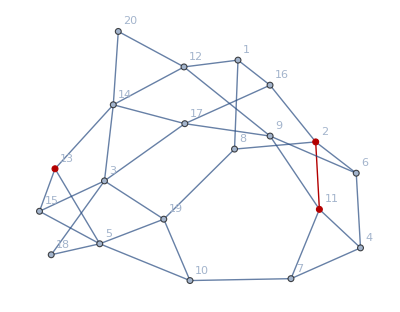

```mathematica
HighlightedGraph = HighlightGraph[mygraph, Subgraph[mygraph, GraphCenter1]]
```

Зададим ребра и вершины из ИДЗ:

```mathematica
w = 16;
e = UndirectedEdge[5,13];
```

Найдем все циклы графа, проходящие через вершину w:

```mathematica
Cycles1 = FindCycle[{mygraph,w}, Infinity,All]
```

Выберем только те циклы, которые содержат ребро e и вершину w

```mathematica
filteredCycles=Select[Cycles1,MemberQ[#,e]&]
```

Наиболее длинный цикл, из отфильтрованного множества:

```mathematica
maxCycle=MaximalBy[filteredCycles,Length]
```

{{16<->2,2<->8,8<->19,19<->10,10<->7,7<->11,11<->4,4<->6,6<->9,9<->17,17<->3,3<->18,18<->5,5<->13,13<->14,14<->20,20<->12,12<->1,1<->16},{16<->2,2<->8,8<->19,19<->10,10<->7,7<->11,11<->4,4<->6,6<->9,9<->17,17<->3,3<->15,15<->5,5<->13,13<->14,14<->20,20<->12,12<->1,1<->16},{16<->1,1<->8,8<->2,2<->6,6<->4,4<->11,11<->7,7<->10,10<->19,19<->3,3<->15,15<->5,5<->13,13<->14,14<->20,20<->12,12<->9,9<->17,17<->16},{16<->1,1<->8,8<->2,2<->6,6<->4,4<->11,11<->7,7<->10,10<->19,19<->3,3<->18,18<->5,5<->13,13<->14,14<->20,20<->12,12<->9,9<->17,17<->16},{16<->1,1<->8,8<->2,2<->6,6<->4,4<->11,11<->7,7<->10,10<->19,19<->5,5<->13,13<->15,15<->3,3<->14,14<->20,20<->12,12<->9,9<->17,17<->16},{16<->2,2<->6,6<->9,9<->11,11<->4,4<->7,7<->10,10<->5,5<->13,13<->15,15<->3,3<->19,19<->8,8<->1,1<->12,12<->20,20<->14,14<->17,17<->16},{16<->2,2<->11,11<->9,9<->6,6<->4,4<->7,7<->10,10<->5,5<->13,13<->15,15<->3,3<->19,19<->8,8<->1,1<->12,12<->20,20<->14,14<->17,17<->16}}

Отобразим циклы на графике:

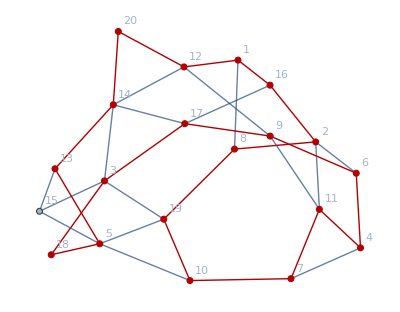

```mathematica
highlightedGraph2=HighlightGraph[mygraph,Graph[maxCycle[[1]]]]
```

С помощью встроенных функций составим поиск в ширину (будем добавлять направленные ребра, достижимые из точки w):

```mathematica
bfsTree = Tree[BreadthFirstScan[mygraph,w]]
```

-Graphics-

Аналогично для поиска в глубину

```mathematica
dfsTree = Tree[DepthFirstScan[mygraph,w]]
```

-Graphics-

Вывод: в результате выполнения задания по анализу графов были составлены представления графа с точностью до изоморфизма, некоторые параметры графа и анализ его связности.  Нахождение простых циклов максимальной длины и обходов в ширину и глубину характеризуют графы.